## Calculate overlap of basis functions.

```mathematica
PhiN = Exp[(-(r-(rcut n)/nmax)^2)/(2 sig^2)]
```

ⅇ^(-(r-(n rcut)/nmax)^2/(2 sig^2))

```mathematica
PhiNPrime = Exp[(-(r-(rcut nprime)/nmax)^2)/(2 sig^2)]
```

ⅇ^(-(r-(nprime rcut)/nmax)^2/(2 sig^2))

```mathematica
SMat = Integrate[r^2*PhiN * PhiNPrime,{r,0,rcut}]//FullSimplify
```

1/(8 nmax^2)ⅇ^(-((n^2+nprime^2) rcut^2)/(2 nmax^2 sig^2)) sig (2 nmax (n+nprime-ⅇ^(((n-nmax+nprime) rcut^2)/(nmax sig^2)) (n+2 nmax+nprime)) rcut sig+ⅇ^(((n+nprime)^2 rcut^2)/(4 nmax^2 sig^2)) √π ((n+nprime)^2 rcut^2+2 nmax^2 sig^2) (Erf[((n+nprime) rcut)/(2 nmax sig)]-Erf[((n-2 nmax+nprime) rcut)/(2 nmax sig)]))

```mathematica
SMat/.{sig->0.5, nmax->14, n->4, nprime->6,rcut->5.0}
```

1.76315

## Calculate overlap between Gaussian and basis function.

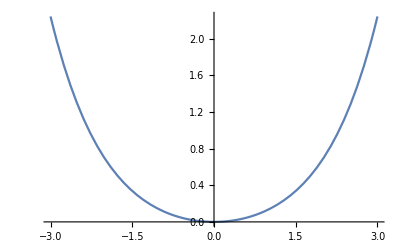

```mathematica
Plot[BesselI[2,x],{x,-3,3}]
```

```mathematica
Integrate[Exp[x]*BesselI[n,x],x]
```

(2^-n x^(1+n) HypergeometricPFQ[{1/2+n,1+n},{2+n,1+2 n},2 x])/((1+n) Gamma[1+n])

```mathematica
PhiN
```

ⅇ^(-(r-(n rcut)/nmax)^2/(2 sig^2))

```mathematica
CFunc = 4 π Exp[-alpha (r^2+ri^2)] BesselI[l,2*alpha*r*ri] Y
```

4 ⅇ^(-alpha (r^2+ri^2)) π Y BesselI[l,2 alpha r ri]

```mathematica
Integrate[CFunc,{r,0,rcut}]
```

∫_0^rcut 4 ⅇ^(-alpha (r^2+ri^2)) π Y BesselI[l,2 alpha r ri]ⅆr

```mathematica
∫_0^rcut 4 ⅇ^(-alpha (r^2+ri^2)-(r-(n rcut)/nmax)^2/(2 sig^2)) π Y BesselI[l,r ]ⅆr
```

```mathematica
PhiN CFunc // FullSimplify
```

4 ⅇ^(-alpha (r^2+ri^2)-(r-(n rcut)/nmax)^2/(2 sig^2)) π Y BesselI[l,2 alpha r ri]

```mathematica
CFunc//FullSimplify
```

4 ⅇ^(-alpha (r^2+ri^2)) π Y BesselI[l,2 alpha r ri]